```mathematica
SetOptions[InputNotebook[], AutoGeneratedPackage->Automatic]
```

# Rearranging the Alphabet!

We’ll start by loading the data sorting the letters in descending order of frequency

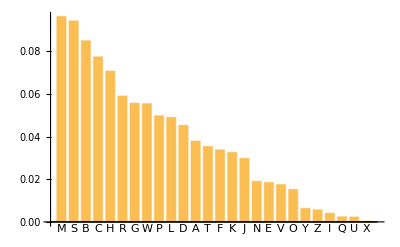

```mathematica
percents = CloudGet["https://www.wolframcloud.com/objects/e338adb3-f090-4867-8456-f3f66c422f38"];
sorted = Reverse@Sort[percents];
BarChart[sorted, ChartLabels->Keys@sorted]
```

We’ll probably want a reverse lookup function for values -> letters

```mathematica
percentsInverse = AssociationThread[Values@percents, Keys@percents];	
ValuesToLetters[list_] := AssociationThread[percentsInverse[#]& /@ list, list]
```

Okay, how do we divide into groups? Here’s a pretty simple idea:

### The Alphabet Bucketing Algorithm

Let’s start with the n largest values--one in each of the n groups--and then iteratively add to the largest remaining value to the group with the smallest total frequency

```mathematica
AddOneToSmallestGroup[groups_, remaining_] := (
	sortedByTotal = Reverse@SortBy[groups, Total@#&];
	totals = Total /@ sortedByTotal;
	nextGreatest = First@remaining;
	next = Append[Most@sortedByTotal, Append[Last@sortedByTotal, nextGreatest]];
	index = First@First@Position[remaining, nextGreatest];
	stillStanding = Delete[remaining, index];
	{ next, stillStanding }
)
```

```mathematica
MakeGroups[n_] := (
	values = Values@Reverse@Sort[percents];
	(* start with the n largest values, one each in n groups *)
	groups = List /@ values[[1;;n]];
	(* and assign the 26-n remaining values *)
	remaining = values[[n + 1;;]];
	While[Length@remaining > 0, (
		{ groups, remaining } = AddOneToSmallestGroup[groups, remaining];
	)];
	letteredGroups = ValuesToLetters /@ groups
)
```

```mathematica
newGroups4 = MakeGroups[4]
totals4 = Total /@ newGroups4
```

{<|C→0.077475,H→0.0708041,L→0.0491037,J→0.0298697,E→0.0185658,Q→0.00241787,U→0.00232247|>,<|M→0.0963997,W→0.0554885,A→0.0379425,T→0.0354322,N→0.0190822,Z→0.00566274|>,<|S→0.0943162,G→0.0557632,D→0.0453413,K→0.0326326,O→0.0152516,Y→0.00634222|>,<|B→0.0850223,R→0.0590957,P→0.0498137,F→0.0338085,V→0.0175313,I→0.00413011,X→0.000384696|>}

{0.250559,0.250008,0.249647,0.249786}

Looking promising! (I swear it’s a coincide that it starts out with the first two letters of my name.) Let’s chart these horizontally to make room for the labels, since this alphabet looks crazy...

```mathematica
SortNewAlphabet[newGroupsN_] := (
	SortBy[Keys[KeySort /@ newGroupsN], First@#&]
)
```

```mathematica
SortLettersByOldAlphabet[newGroups_] := SortBy[KeySort /@ newGroups, First@Keys@#&]
```

```mathematica
ChartGroups[newGroups_, width_:800] := (
	MakeChart[newGroups, Keys@newGroups, width]
)
```

```mathematica
ChartGroupsSorted[newGroups_, width_:800] := (
	sortedNewGroups = SortLettersByOldAlphabet[newGroups];
	sortedAlphabet = SortNewAlphabet[newGroups];
	MakeChart[sortedNewGroups, sortedAlphabet, width]
)
```

```mathematica
MakeChart[buckets_, sortedAlphabet_, width_] := (
	labeled = Labeled[#, Style[ToString@Round[100. * Total@#, 0.01] <> "%", FontSize->14], Above]& /@ buckets;
	BarChart[
		Reverse@labeled,
		BarSpacing->0.8 * 800 / width,
		BarOrigin->Left,
		ChartLayout->"Stacked",
		ChartLabels->Placed[Style[#, LightGray, 12]& /@ Flatten@Reverse@Keys@buckets, Center],
		ChartStyle->"Rainbow",
		AspectRatio->0.25 * Sqrt@Length@buckets,
		ImageSize->width,
		PlotLabel->Row[Framed /@ First@Style[StringRiffle[#, ","]& /@ sortedAlphabet, FontSize->width / 32, Black, Bold]]
	]
)
```

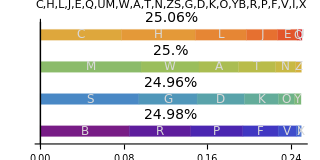

```mathematica
ChartGroups[newGroups4, 320]
```

MUCH better! Just out of curiosity, let’s see how it performs with more or fewer tables

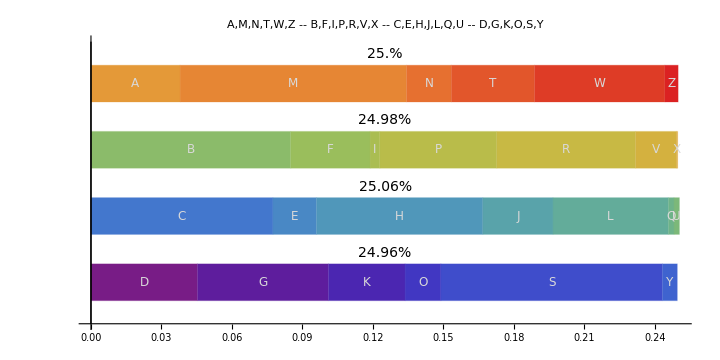

```mathematica
ChartGroupsSorted[newGroups4, 720]
```

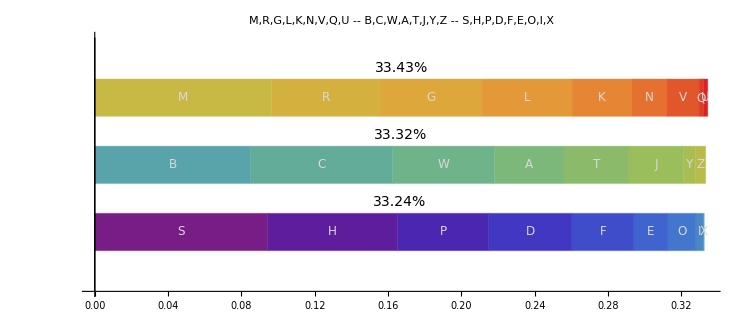

```mathematica
ChartGroups[MakeGroups[3], 750]
```

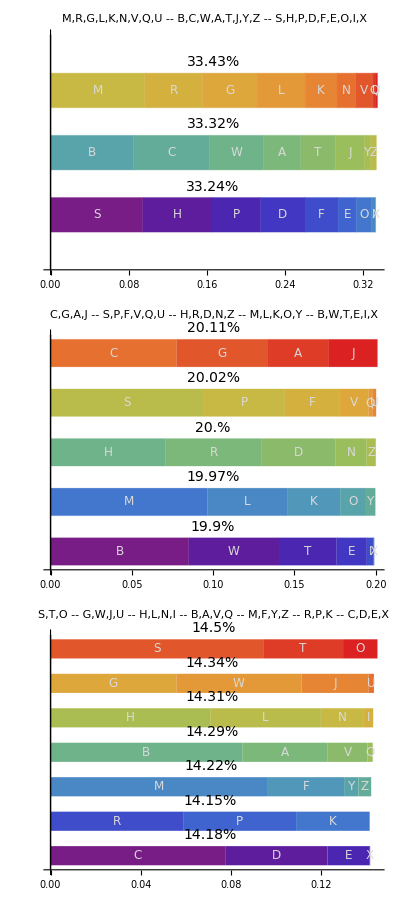

```mathematica
Column[{
	ChartGroups[MakeGroups[3], 500],
	ChartGroups[MakeGroups[5], 500],
	ChartGroups[MakeGroups[7], 500]
}]
```

It works great for up to at least seven tables! Let’s make some placards for four tables. We’ll sort the letters within each group alphabetically for the sake of the volunteers at the desk, and then sort the groups by the first letter.

```mathematica
newAlphabetSorted4 = SortNewAlphabet[newGroups4];
Flatten@newAlphabetSorted4
```

{A,M,N,T,W,Z,B,F,I,P,R,V,X,C,E,H,J,L,Q,U,D,G,K,O,S,Y}

But first, I think we need to sing it

```mathematica
newSong = Import["audio/newAlphabetSung.mp3", "MP3"]
```

### Okay, let’s make signs

```mathematica
MakePlacard[newAlphabetSortedN_] := (
	sequences = StringRiffle[#, ","]& /@ newAlphabetSortedN;
	Column[Framed[Column[Flatten@{
		Style[#, 14, Darker@Gray]& /@ {"Please queue here for", "last names beginning with" },
		Style[#, 36]
	}, Center, Spacings->1], FrameMargins->{{20,20},{20,16}}, RoundingRadius->5, ImageSize->400, Alignment->Center]& /@ sequences]
)
```

```mathematica
MakePlacard[newAlphabetSorted4]
```

Please queue here for
last names beginning with
A,M,N,T,W,Z
Please queue here for
last names beginning with
B,F,I,P,R,V,X
Please queue here for
last names beginning with
C,E,H,J,L,Q,U
Please queue here for
last names beginning with
D,G,K,O,S,Y